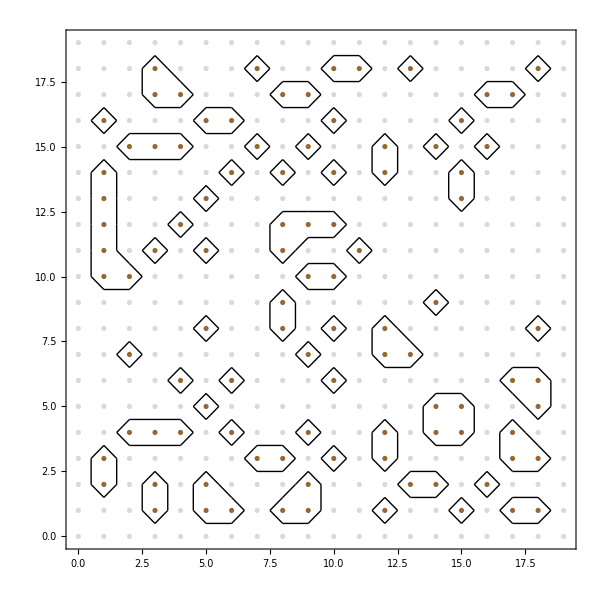

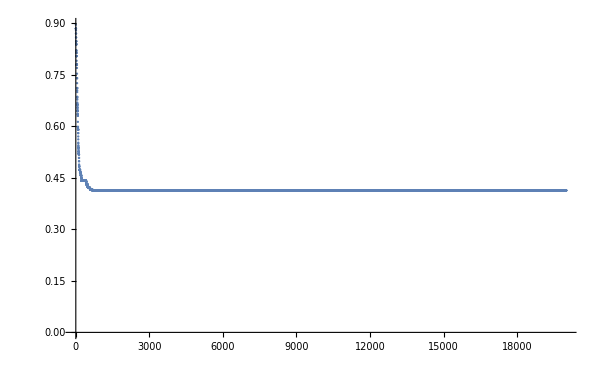

```mathematica
infoData=Import[NotebookDirectory[]<>"out/x64-Release/output-info.txt","Table"];

data=Import[NotebookDirectory[]<>"out/x64-Release/output-boundary.txt","Table"];
data=Partition[#,2]&/@data;

rawdata=Import[NotebookDirectory[]<>"out/x64-Release/output-raw.txt","Table"];
disks=MapIndexed[{If[#1==1,Brown,LightGray],Disk[#2-{1,1},0.1]}&,Transpose@rawdata,{2}];

Graphics[{disks,Line[data]},ImageSize->600,Frame->True]

ListPlot[infoData,PlotRange->All]
```

```mathematica
BinaryReadList[NotebookDirectory[]<>"out/x64-Release/test.bin", "UnsignedInteger64",1]
```

{234}

```mathematica
Join[Table["Real64",9],Table["Integer32",2]]
```

{Real64,Real64,Real64,Real64,Real64,Real64,Real64,Real64,Real64,Integer32,Integer32}

```mathematica
file = OpenRead[filename, BinaryFormat->True];
d=First@BinaryReadList[file, "Integer32",1];
```

```mathematica
LoadCube[filename_]:=Module[{d,dims,dataAndHeaders},
file = OpenRead[filename, BinaryFormat->True];
d=First@BinaryReadList[file, "UnsignedInteger64",1];
dims=BinaryReadList[file, "UnsignedInteger64",d];
Print["Dimensions: ",dims];
dataAndHeaders=TakeDrop[BinaryReadList[file, "Real64"],Times@@dims];
Close[file];
{ArrayReshape[dataAndHeaders[[1]],dims],TakeList[dataAndHeaders[[2]],dims]}]
```

```mathematica
(*Particle Indices are: x,y, velX,velY, dens, press, intEnergy, kinEnergy, Dummy, group, id*)
(*Solid Indices are: x,y, velX,velY, angle, angVel, dragForce, group*)
```

Dimensions: {338,1,9}

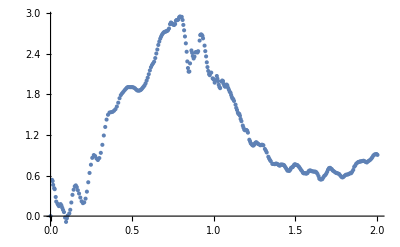

```mathematica
(*Show the drag force*)
{solids,headers}=LoadCube[NotebookDirectory[]<>"out/x64-Release/solids.binary"];
ma=MovingAverage[Transpose[{headers[[1]],solids[[All,1,7]]}],1];
ListPlot[ma,PlotRange->All]
```

```mathematica
{partics, headers}=LoadCube[NotebookDirectory[]<>"out/x64-Release/particles.binary"];
groupCols={RGBColor[0.49, 0.63, 0.96],Black};
Manipulate[Graphics[{groupCols[[#[[10]]+1]],Disk[#[[{1,2}]],0.005]}&/@partics[[i]], PlotRange->{{0,1},{0,1}},Frame->True,AspectRatio->1,ImageSize->600],{i,1,Length@partics,1}]
```

Dimensions: {340,407,11}

Dimensions: {597,407,11}

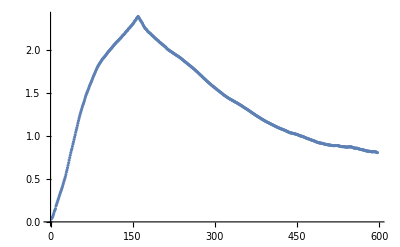

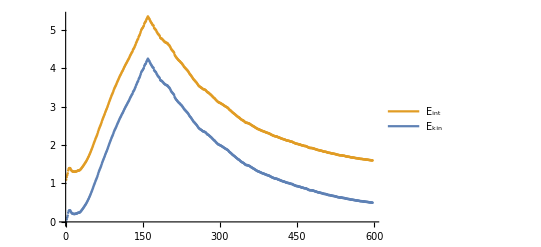

```mathematica
{partics, headers}=LoadCube[NotebookDirectory[]<>"out/x64-Release/particles.binary"];

ListPlot[Total[partics[[All,All,3]],{2}]/Dimensions[partics][[2]],PlotRange->All]
ListPlot[{Total[partics[[All,All,8]],{2}],Total[partics[[All,All,7]],{2}]},PlotLayout->"Stacked",PlotLegends->{"E_kin","E_int"}]
```

```mathematica
Manipulate[ListDensityPlot[{#[[1]],#[[2]],#[[5]]}&/@partics[[i]], PlotRange->{{0,1},{0,1},All},
Mesh->All,InterpolationOrder->0,ColorFunction->ColorData[{"Rainbow",{0.5,2.0}}],ColorFunctionScaling->False,ClippingStyle->Automatic,
PlotLegends->Automatic,Frame->True,AspectRatio->1,ImageSize->600],{i,1,Length@partics,1},TrackedSymbols:>{i}]
```

Part::partw: Part 597 of {{{0.0098,0.0545,0.,0.,2.12846,2.12846,0.0025,0.,0.,0.,«1»},{0.012,0.206,0.,0.,2.129,2.129,0.0025,0.,0.,0.,«1»},«7»,{0.1107,0.064,0.,0.,2.31591,2.31591,0.0025,0.,0.,0.,«1»},«397»},«9»,«330»} does not exist.

Part::partd: Part specification 597⟦1⟧ is longer than depth of object.

Part::partd: Part specification 597⟦2⟧ is longer than depth of object.

Part::partd: Part specification 597⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {597⟦1⟧,597⟦2⟧,597⟦5⟧} cannot be used as a part specification.

ListDensityPlot::arrayerr: {{{0.0098,0.0545,0.,0.,2.12846,2.12846,0.0025,0.,0.,0.,«1»},{0.012,0.206,0.,0.,2.129,2.129,0.0025,0.,0.,0.,«1»},«7»,{0.1107,0.064,0.,0.,2.31591,2.31591,0.0025,0.,0.,0.,«1»},«397»},{«1»},{{0.00616776,0.0495955,«7»,0.,«1»},«9»,«397»}}⟦{«1»}⟧ must be a valid array.